```mathematica
folder="C:\\Users\\WizardOf\\Documents\\Visual Studio 2013\\Projects\\ParallelComputingHomeworkII\\ex02"
```

C:\Users\WizardOf\Documents\Visual Studio 2013\Projects\ParallelComputingHomeworkII\ex02

## Variation of Matrix size

```mathematica
sizes={2,16,256,1024};
```

```mathematica
s=(Import[FileNameJoin[{folder, "cuda_"<>ToString[#]<>"_2.out"}]]⟦All,2⟧)&/@sizes
```

{{0.,0.000071,0.000034},{0.000036,0.000074,0.000037},{0.163386,0.004978,0.005711},{12.5554,0.35926,0.377693}}

```mathematica
cpu=MapThread[{#1,#2}&,{sizes,s⟦All,1⟧}]
```

{{2,0.},{16,0.000036},{256,0.163386},{1024,12.5554}}

```mathematica
gpuGlobal=MapThread[{#1,#2}&,{sizes,s⟦All,2⟧}]
```

{{2,0.000071},{16,0.000074},{256,0.004978},{1024,0.35926}}

```mathematica
gpuShared=MapThread[{#1,#2}&,{sizes,s⟦All,3⟧}]
```

{{2,0.000034},{16,0.000037},{256,0.005711},{1024,0.377693}}

```mathematica
Grid[{cpu⟦All,1⟧,cpu⟦All,2⟧,gpuGlobal⟦All,2⟧,gpuShared⟦All,2⟧}, Frame->All]
```

2 | 16 | 256 | 1024
0. | 0.000036 | 0.163386 | 12.5554
0.000071 | 0.000074 | 0.004978 | 0.35926
0.000034 | 0.000037 | 0.005711 | 0.377693

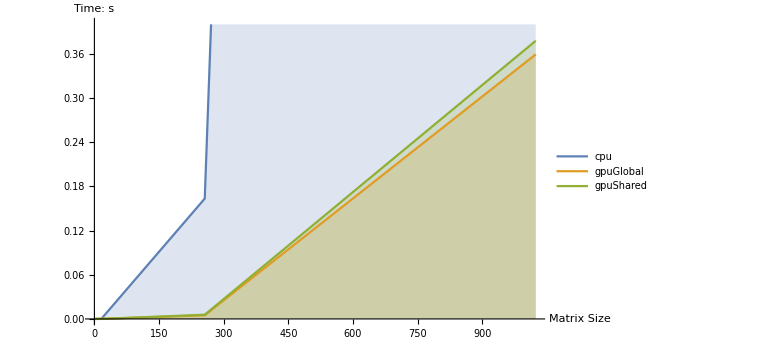

```mathematica
ListPlot[{cpu,gpuGlobal,gpuShared}, Joined->True,Filling->Axis,PlotRange->{{0,1024},{0,0.4}},PlotLegends->{"cpu","gpuGlobal","gpuShared"},AxesLabel->{"Matrix Size", "Time: s"},ImageSize->Large]
```

## Variation of Block Size (Matrix Size: 1024)

```mathematica
sizes={2,4,8,16,32};
```

```mathematica
s=(Import[FileNameJoin[{folder, "cuda_1024_"<>ToString[#]<>".out"}]]⟦All,2⟧)&/@sizes
```

{{12.5554,0.35926,0.377693},{12.5529,0.105965,0.068},{12.5637,0.04009,0.019607},{12.5663,0.027075,0.013327},{12.5854,0.024356,0.011233}}

```mathematica
cpu=MapThread[{#1,#2}&,{sizes,s⟦All,1⟧}]
```

{{2,12.5554},{4,12.5529},{8,12.5637},{16,12.5663},{32,12.5854}}

```mathematica
gpuGlobal=MapThread[{#1,#2}&,{sizes,s⟦All,2⟧}]
```

{{2,0.35926},{4,0.105965},{8,0.04009},{16,0.027075},{32,0.024356}}

```mathematica
gpuShared=MapThread[{#1,#2}&,{sizes,s⟦All,3⟧}]
```

{{2,0.377693},{4,0.068},{8,0.019607},{16,0.013327},{32,0.011233}}

```mathematica
Grid[{cpu⟦All,1⟧,cpu⟦All,2⟧,gpuGlobal⟦All,2⟧,gpuShared⟦All,2⟧}, Frame->All]
```

2 | 4 | 8 | 16 | 32
12.5554 | 12.5529 | 12.5637 | 12.5663 | 12.5854
0.35926 | 0.105965 | 0.04009 | 0.027075 | 0.024356
0.377693 | 0.068 | 0.019607 | 0.013327 | 0.011233

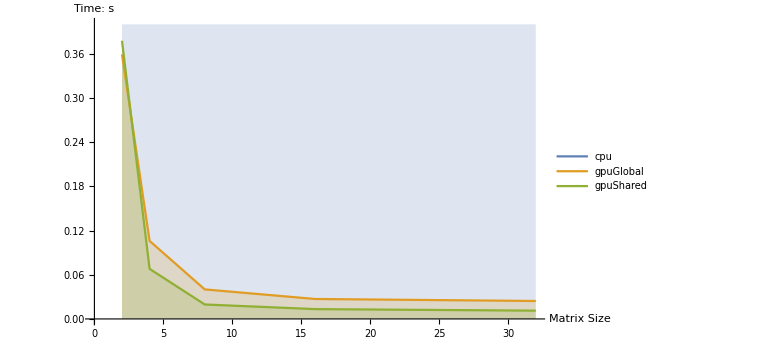

```mathematica
ListPlot[{cpu,gpuGlobal,gpuShared}, Joined->True,Filling->Axis,PlotRange->{{0,32},{0,0.4}},PlotLegends->{"cpu","gpuGlobal","gpuShared"},AxesLabel->{"Matrix Size", "Time: s"},ImageSize->Large]
```